```mathematica
ClearAll["Global`*"];SetDirectory[NotebookDirectory[]];

<<ManipulatePrepare.m;
DrawPSPhaseDiagramcOnly[𝓂MaxPlot_,𝓂MaxMaxPlot_,𝒸MaxPlot_] := Block[{},
DrawDiagrams[𝓂MaxPlot,𝓂MaxMaxPlot,𝒸MaxPlot];
𝒸PlotDashing = restylePlot[𝒸Plot,{Dashing[Small]}];
TractableBufferStockPhaseDiag=Show[
𝒸PlotDashing
(*,Ticks->None*)
,AxesLabel->{"\!\(\*SubsuperscriptBox[\(𝓂\), \( \), \(e\)]\)","\!\(\*SubsuperscriptBox[\(𝒸\), \( \), \(e\)]\)"}
,AxesOrigin->{-Severance/ℛ,0.}
,PlotRange->{{-Severance/ℛ,𝓂MaxPlot},{0,𝒸MaxPlot}}]
];
```

```mathematica
??c*
```

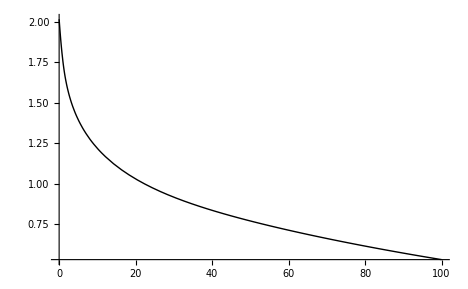

```mathematica
cPlotBase=Plot[cEPF[𝓂]-cE[𝓂],{𝓂,0,100}]
```

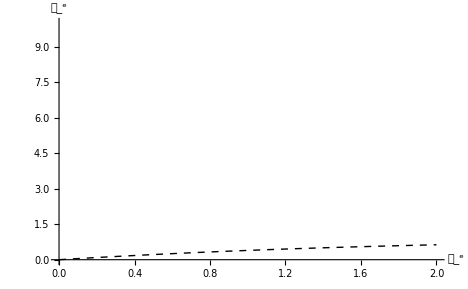

```mathematica
DrawPhaseDiagramcOnly[2,3,10]
```

## Manipulate℧

## Low

```mathematica
FindStableArm;{𝓂Max,𝓂MaxMax}={20,100}𝓂E //N;
Manipulate[
Block[{$PerformanceGoal="Speed",℧,℧Base},
℧=℧Slider;If[((R) β)^(1/ρ)/Γ ≥  1||((R) β)^(1/ρ)/(R) ≥  1,Style[Text["Impatience Condition Not Satisfied."],24]];
DrawPSPhaseDiagram[𝓂Max,𝓂MaxMax,𝒸Max]
],{{℧Slider,0.01,"℧"},0.001,0.01,0.001}]
```

```mathematica
℧=℧Base
```

0.005

```mathematica
??ExportFigsToDir
```

Global`ExportFigsToDir

ExportFigsToDir[FigName_,DirNameForFigs_]:=Block[{},Print[Show[ToExpression[FigName]]];Print[Exporting figure to <>DirNameForFigs<>SubDirectoryString<>FigName<>.xxx];Export[DirNameForFigs<>SubDirectoryString<>FigName<>.eps,ToExpression[FigName],EPS];Export[DirNameForFigs<>SubDirectoryString<>FigName<>.jpg,ToExpression[FigName],JPG];Export[DirNameForFigs<>SubDirectoryString<>FigName<>.png,ToExpression[FigName],PNG,ImageSize→FullPageSize];Export[DirNameForFigs<>SubDirectoryString<>FigName<>.svg,ToExpression[FigName],SVG];Export[DirNameForFigs<>SubDirectoryString<>FigName<>.pdf,ToExpression[FigName],PDF];If[OpenFigsUsingShell≠False,Run[open <>DirNameForFigs<>SubDirectoryString<>FigName<>.pdf]];]

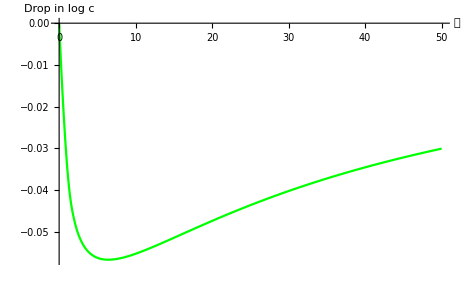

Exporting figure to /Volumes/Data/Job/Keynotes/2017-12_RBNZ-HeteroMacro/Figures/sChangeWhenUncertGoesUp.xxx

```mathematica
𝓂MaxMultiple=50;
℧=℧Base;
FindStableArm;
cEInterp℧Base=cEInterp;
℧=2 ℧Base ;
FindStableArm
cEInterp℧Big=cEInterp;
sChangeWhenUncertGoesUp=Plot[{(cEInterp℧Big[𝓂]-cEInterp℧Base[𝓂])/cEPF[𝓂]},{𝓂,0,50},PlotStyle->{Red,Green},AxesLabel->{"𝓂","Drop in log c"},Ticks->{None,Automatic}];
ExportFigsToDir["sChangeWhenUncertGoesUp","/Volumes/Data/Job/Keynotes/2017-12_RBNZ-HeteroMacro/Figures"]
```

```mathematica
??cEPF
```

Global`cEPF

cEPF[𝓂_]:=(𝓂-(1-SoiTax)+𝔥) κ

```mathematica
𝔥
```

```mathematica
κ
```

0.0605254

```mathematica
cEInterpBase[2]
```

0.631506

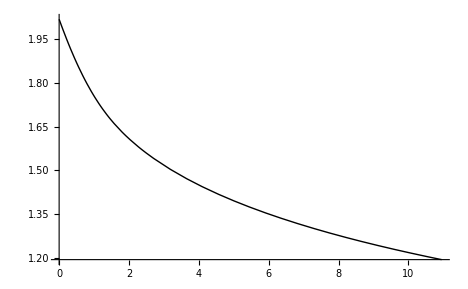

```mathematica
Show[𝓈Plot]
```

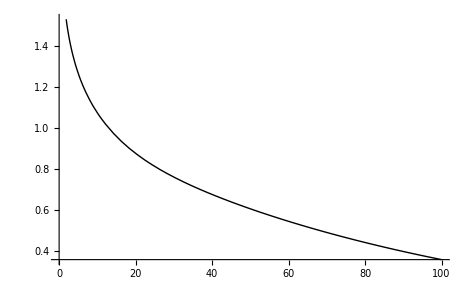

```mathematica
DrawPSPhaseDiagram[100,150,2];Show[𝓈Plot]
```

```mathematica
DrawPSDiagrams[100,150,2];Show[𝓈Plot]
```

-Graphics-

```mathematica
0
```

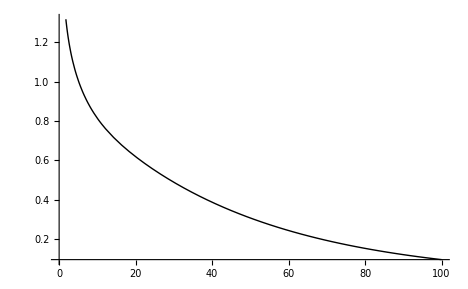

```mathematica
𝓈Plot=Plot[cEPF[𝓂]-cE[𝓂],{𝓂,-Severance/ℛ,100}]
```